# Inlämningsuppgift 2

Magnus Fredriksson, TIDAB, magfred@kth.se
Fredrik Öberg, TIDAB, fobe@kth.se

Uppgift: Analysera uppmätt data.

## Sammanfattning

### Uppgift

Uppgiften bestod i att analysera uppmätt signalstyrka från en WiFi-accesspunkt. Utifrån mätningarna skulle därefter en lämplig matematisk modell tas fram.

### Resultat

En mängd data hade uppmätts på 20 olika avstånd från accesspunkten med intervall på 5 meter. Avstånden var därmed 5-100 meter från accesspunkten. För att hantera den stora variationen på signalstyrkan mättes värdena flera gånger från varje mätpunkt. Därmed ansåg gruppen det rimligt att skapa medelvärden på den uppmätta datan. 
För att enkelt kunna beräkna medelvärdet formaterades datan om så att den representerades som en lista med varje mätningssekvens som en underlista. Detta gjorde att medelvärdet kunde beräknas för varje mätpunkt och gav dessa värden:

{{5,6.35372×10^-6},{10,4.0763×10^-7},{15,1.10993×10^-7},{20,5.61165×10^-8},{25,2.43562×10^-8},{30,9.28937×10^-9},{35,1.28464×10^-8},{40,5.58308×10^-9},{45,5.74365×10^-9},{50,3.69663×10^-9},{55,1.09628×10^-9},{60,1.21276×10^-9},{65,1.12077×10^-9},{70,7.7993×10^-10},{75,4.52623×10^-10},{80,2.12614×10^-10},{85,2.09058×10^-10},{90,1.3306×10^-10},{95,1.72124×10^-10},{100,2.82954×10^-10}}

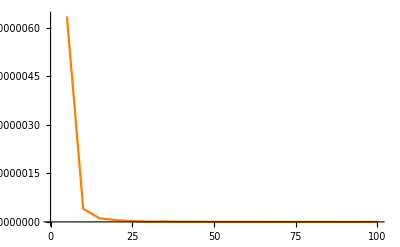
Datan för medelvärdena skrevs sedan ut i en graf för att visuellt kunna anlyseras. Y-axeln ritades linjärt för att förenkla visualiseringen.

-Graphics-

En matematisk modell av grafen kunde nu konstrueras. Matematisk intuition användes för att hitta en tänkbar modell för den represantativa grafen för medelvärdena. Egenskaperna hos grafen för mätpunkterna där Y-värdena blir väldigt stora när X går mot 0, och snabbt avtagande som X ökar, men inte verkar inte nå 0 eller mindre, tyder på en funktion enligt modellen: 

		a /x^b

Modellen testades genom funktionen FindFit där Mathematica användes för att hitta de specifika instanser av a och b  som ger en graf som väl överrensstämmer med de uppmätta värdena.

		0.00347167/x^3.91653

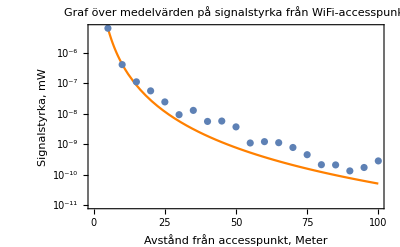
De av funktionen givna konstanterna sattes in i uttrycket och ritades ut tillsammans med de av oss skapade medelvärdena. Y-axeln definierades logaritmisk för att få ett tydligare resultat. Detta gav oss visualiseringen:

-Graphics-

## Kod

```mathematica
ClearAll["`*"]
```

### Datan från mätningarna läggs in

```mathematica
data={{5,4.2180506341246474*^-6},{10,8.52072632483756*^-8},{15,1.9122244963644555*^-7},{20,4.583863072516606*^-8},{25,8.138004722270266*^-9},{30,1.5236067293781787*^-9},{35,1.9689607977818997*^-8},{40,1.0356015584142407*^-9},{45,5.1171329242687634*^-9},{50,1.3150023891748594*^-9},{55,2.75925031324734*^-10},{60,6.44739787013969*^-10},{65,1.269501699841764*^-9},{70,3.368354766378623*^-11},{75,2.882696661780091*^-11},{80,2.4182183464215087*^-10},{85,3.982588451684898*^-10},{90,6.737749787589035*^-11},{95,8.116170964273532*^-11},{100,6.030125496210169*^-10},{5,2.1476267234440643*^-6},{10,2.3244825805810026*^-6},{15,1.376564833236655*^-7},{20,2.972699644181631*^-8},{25,4.737092876342727*^-8},{30,8.191016754218927*^-9},{35,8.898775290782262*^-9},{40,6.666360149797248*^-9},{45,7.417481547646882*^-10},{50,1.739062622942222*^-9},{55,4.842018315239307*^-10},{60,6.521126861389932*^-10},{65,1.3985827036122423*^-9},{70,1.492147178019141*^-10},{75,4.2134547161500933*^-10},{80,6.831201201202558*^-11},{85,1.0802444285398891*^-10},{90,1.820839088556722*^-11},{95,1.7132267011413344*^-10},{100,3.754919516870398*^-10},{5,0.00001044694319643655},{10,5.69674157685483*^-8},{15,8.315750786932738*^-8},{20,1.0019648005036426*^-7},{25,5.5374731613526704*^-8},{30,1.9485705516272266*^-9},{35,1.0113888568168166*^-8},{40,1.7883852014284595*^-10},{45,1.3475441439488888*^-9},{50,9.038105865797945*^-9},{55,1.5816145773480966*^-9},{60,9.346731416982425*^-10},{65,1.9747183113229924*^-10},{70,7.813851506825158*^-10},{75,1.8343422005958098*^-10},{80,2.432821218173799*^-11},{85,4.1395116687213914*^-10},{90,2.1055234143168004*^-10},{95,7.072714932230835*^-10},{100,1.0580839584733221*^-10},{5,2.5798845260889457*^-6},{10,2.3232081111840804*^-7},{15,2.667892232508383*^-7},{20,1.682870319735423*^-7},{25,1.0484611243537326*^-8},{30,5.680186101488732*^-9},{35,4.835436533411094*^-9},{40,4.3318993920735265*^-10},{45,1.4476913311872237*^-8},{50,1.8412321693611577*^-9},{55,1.2250442659732012*^-9},{60,1.2394579016661714*^-9},{65,1.3640777227973738*^-9},{70,2.233313125797408*^-9},{75,2.0888533393477414*^-10},{80,1.9447658506520675*^-10},{85,1.3846095194972496*^-10},{90,1.274324549282506*^-10},{95,8.450766454310523*^-12},{100,6.298694843322194*^-10},{5,5.064138651648234*^-6},{10,7.421893655109317*^-8},{15,6.899580135924716*^-8},{20,8.341725253025645*^-9},{25,3.2432622035577643*^-9},{30,9.402559699099224*^-10},{35,6.667022356411859*^-9},{40,1.3887713695363457*^-8},{45,4.067975610974101*^-9},{50,2.130756764244549*^-9},{55,5.876054330139342*^-10},{60,5.5580351570704426*^-9},{65,1.1925382281657626*^-11},{70,3.307998125545722*^-10},{75,3.8655748988116185*^-10},{80,1.0067273465424143*^-11},{85,1.0708274713929411*^-10},{90,3.8222332586554166*^-10},{95,6.528819437769106*^-11},{100,4.577643994791942*^-10},{5,6.3069218582484736*^-9},{10,3.496119937611541*^-7},{15,1.5524046006115388*^-7},{20,1.348710877120591*^-7},{25,1.744500035260079*^-8},{30,1.6603294248904193*^-8},{35,2.5206405116488415*^-8},{40,1.4639960586270222*^-9},{45,5.5464045166870474*^-9},{50,9.786485003821449*^-9},{55,8.912516353001634*^-10},{60,1.471096625592371*^-9},{65,1.1946582824950649*^-9},{70,1.986770813327404*^-10},{75,8.73810462167828*^-10},{80,1.481836574016208*^-10},{85,1.9717731215993406*^-10},{90,2.5542691844114277*^-10},{95,1.870296630801057*^-10},{100,4.8814658856710215*^-11},{5,2.5900661319482445*^-6},{10,1.0780841918704108*^-7},{15,4.655536564862844*^-8},{20,2.543054652487668*^-8},{25,6.270341785015637*^-9},{30,7.91889292098162*^-9},{35,4.5637976602144815*^-9},{40,8.356921214604936*^-9},{45,1.6718361654608334*^-8},{50,2.2999294061801205*^-9},{55,1.6126339340916615*^-9},{60,2.0568855673703833*^-10},{65,6.052576150395791*^-10},{70,5.877640181357158*^-11},{75,4.6109719347766947*^-10},{80,1.782630507857206*^-11},{85,3.4094504242364744*^-11},{90,2.1521641486957376*^-11},{95,1.7693465429181382*^-10},{100,1.108152605829104*^-10},{5,3.1556932003850125*^-6},{10,3.150971172099647*^-7},{15,9.943829214376952*^-8},{20,2.1072930805682054*^-9},{25,7.871904774251177*^-8},{30,1.6866458826162318*^-8},{35,4.795657356481652*^-9},{40,5.333511697714692*^-10},{45,7.4482115262124705*^-9},{50,2.867301230543851*^-9},{55,1.718421442391107*^-10},{60,9.530175559071542*^-11},{65,8.064075761687711*^-11},{70,1.0288790220335421*^-9},{75,1.2003435795735374*^-9},{80,1.0355412440290074*^-9},{85,3.174113486780833*^-10},{90,1.2641498504598634*^-10},{95,7.976882480327851*^-11},{100,1.5880932014212394*^-11},{5,1.8876456584927902*^-6},{10,5.712603557548288*^-8},{15,1.0409753913422592*^-8},{20,3.70525719392294*^-9},{25,7.217910793655984*^-9},{30,2.6859651963882603*^-8},{35,1.7334341745842147*^-8},{40,1.6478052352150378*^-8},{45,8.832989797645319*^-10},{50,5.2800718896975975*^-9},{55,2.9356332556024264*^-9},{60,8.311194232224003*^-10},{65,2.3482950370701028*^-9},{70,6.609181455148873*^-10},{75,6.687310253639731*^-10},{80,2.0450137423633253*^-10},{85,1.8597772765870776*^-13},{90,5.506236237381463*^-11},{95,4.3327792764759966*^-11},{100,1.7172396826556043*^-10},{5,0.00003144088668999315},{10,4.7345842694168693*^-7},{15,5.046679805107057*^-8},{20,4.2660259390362525*^-8},{25,9.298404264634156*^-9},{30,6.361737533444243*^-9},{35,2.635880341166212*^-8},{40,6.796773705779885*^-9},{45,1.0889152233121153*^-9},{50,6.683153680905807*^-10},{55,1.197038904676683*^-9},{60,4.953273024900673*^-10},{65,2.7372783025689915*^-9},{70,2.3236548538241373*^-9},{75,9.319688689447546*^-11},{80,1.8108111597248558*^-10},{85,3.759319337869303*^-10},{90,6.638019323373417*^-11},{95,2.0068801250795827*^-10},{100,3.103631692890908*^-10}};
```

### Datan analyseras och bearbetas

```mathematica
formattedArray=ArrayReshape[data,{10,20,2}];
```

```mathematica
mean=Mean[formattedArray];
```

```mathematica
pMean = ListPlot[mean, Joined -> True, PlotRange->{{Automatic, 100}, {Automatic, mean[[1,2]]}}, PlotStyle->{Orange}];
```

```mathematica
model=a/(x)^b;
expr = model /.FindFit[mean,model,{a,b},x];
```

```mathematica
range ={{0, 100}, {10^-11, mean[[1,2]]}} ;
pExpr = LogPlot[expr,{x,0,100},PlotRange -> range,
Frame->True,
 FrameLabel->{"Avstånd från accesspunkt, Meter","Signalstyrka, mW"},
PlotLabel->"Graf över medelvärden på signalstyrka från WiFi-accesspunkt",
PlotStyle->{Orange}];
pMean = ListLogPlot[mean, PlotRange -> range];
Show[{pExpr, pMean}];
```